```mathematica
α=0.01
```

0.01

```mathematica
Ω=1
```

1

```mathematica
β=1
```

1

```mathematica
Subscript[ω, c]=100
```

100

```mathematica
ω'=5
```

5

```mathematica
f1[k_]=α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k-(Ω+ω'))
```

(0.0025 ⅇ^(-k/100) k Coth[k/2])/(-6+k)

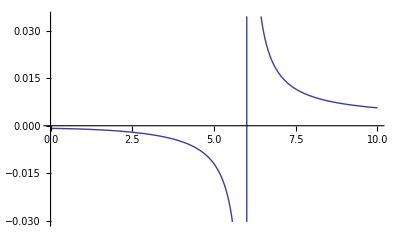

```mathematica
Plot[f1[k],{k,0,10}]
```

```mathematica
i1 = NIntegrate[f1[k],{k,3*(Ω+ω')/2,∞}]
```

0.270286

```mathematica
i2 = NIntegrate[f1[k],{k,0,(Ω+ω')/2}]
```

-0.0043246

```mathematica
i3 = NIntegrate[f1[k],{k,(Ω+ω')/2,(Ω+ω')-0.00001}]
```

-0.172672

```mathematica
i4 = NIntegrate[f1[k],{k,(Ω+ω')+0.00001,3*(Ω+ω')/2}]
```

0.185471

```mathematica
Subscript[i, tot]=i1+i2+i3+i4
```

0.278761

```mathematica
f2[k_]=-α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k-(ω'-Ω))
```

-(0.0025 ⅇ^(-k/100) k Coth[k/2])/(-4+k)

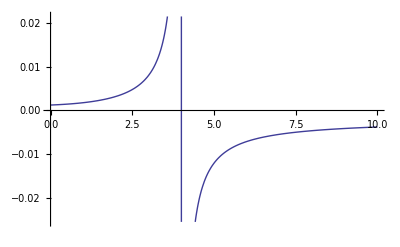

```mathematica
Plot[f2[k],{k,0,10}]
```

```mathematica
Subscript[l, 1]=NIntegrate[f2[k],{k,3*(ω'-Ω)/2,∞}]
```

-0.267701

```mathematica
Subscript[l, 2]=NIntegrate[f2[k],{k,0,(ω'-Ω)/2}]
```

0.00385695

```mathematica
Subscript[l, 3]=NIntegrate[f2[k],{k,(ω'-Ω)/2,(ω'-Ω)-10^-4}]
```

0.0948712

```mathematica
Subscript[l, 4]=NIntegrate[f2[k],{k,(ω'-Ω)+10^-4,3*(ω'-Ω)/2}]
```

-0.102863

```mathematica
Subscript[l, tot]=Subscript[l, 1]+Subscript[l, 2]+Subscript[l, 3]+Subscript[l, 4]
```

-0.271836

```mathematica
f3[k_]=-α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k+ω'+Ω)
```

-(0.0025 ⅇ^(-k/100) k Coth[k/2])/(6+k)

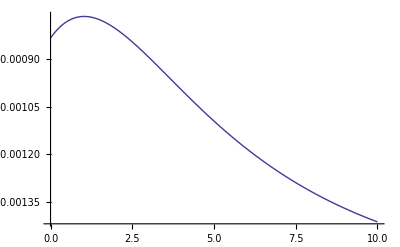

```mathematica
Plot[f3[k],{k,0,10}]
```

```mathematica
NIntegrate[f3[k],{k,0,∞}]
```

-0.214559

```mathematica
f4[k_]=α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k+ω'-Ω)
```

(0.0025 ⅇ^(-k/100) k Coth[k/2])/(4+k)

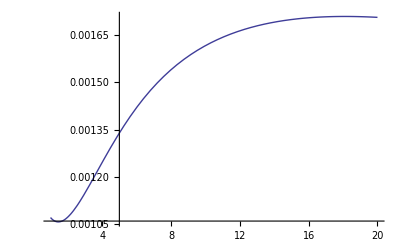

```mathematica
Plot[(0.0025 ⅇ^(-k/100) k Coth[k/2])/(4+k),{k,1,20}]
```

```mathematica
NIntegrate[f4[k],{k,0,∞}]
```

0.223655

```mathematica
Subscript[i, tot]+Subscript[l, tot]+NIntegrate[f3[k],{k,0,∞}]+NIntegrate[f4[k],{k,0,∞}]
```

0.0160199

```mathematica
f[k_]=f1[k]+f2[k]+f3[k]+f4[k]
```

(0.0025 ⅇ^(-k/100) k Coth[k/2])/(-6+k)-(0.0025 ⅇ^(-k/100) k Coth[k/2])/(-4+k)+(0.0025 ⅇ^(-k/100) k Coth[k/2])/(4+k)-(0.0025 ⅇ^(-k/100) k Coth[k/2])/(6+k)

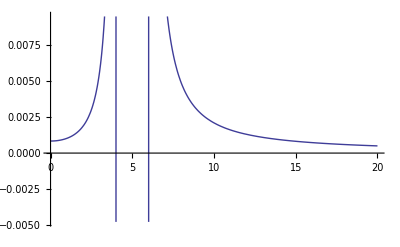

```mathematica
Plot[f[k],{k,0,20}]
```

```mathematica
Regcs=NIntegrate[f3[k],{k,0,∞}]-Subscript[l, tot]-NIntegrate[f4[k],{k,0,∞}]+Subscript[i, tot]
```

0.112383